# Data analysis of Open Dynamics

```mathematica
SetDirectory[NotebookDirectory[]];
datawigner=Import["output/test_wignerquartic.dat"];
wg=Import["output/wignerresults.dat"];
datasp=Import["output/survivalprobability.dat"];
datale=Import["output/loschmidt_echo.dat"];
```

#### Classical Trajectories

```mathematica
(*Classical Hamiltonian*)
Δ=-2;
ϵ=0.0;
Kp=1;
ω=17.1;
ξ=0.5;
H[q_,p_,t_]=-(Δ/2)*(q^2+p^2)+(Kp/4)*(q^2+p^2)^2-ϵ*(q^2-p^2);
HD[q_,p_,t_]=-(Δ/2)*(q^2+p^2)+(Kp/4)*(q^2+p^2)^2-ϵ*(q^2-p^2)+ξ*(q^2+p^2)*Cos[ω*t]/2;
```

```mathematica
(*Solving the Hamiltons equation*)
pin=3.0;
qin=-3;
tf=20000;
T=2 Pi/ω;
sol=NDSolve[{D[q[t],t]==D[H[q[t],p[t],t],p[t]],D[p[t],t]==-D[H[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
solt=NDSolve[{D[q[t],t]==D[HD[q[t],p[t],t],p[t]],D[p[t],t]==-D[HD[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
```

```mathematica
(*Classical trajectories and Poncaire sections*)
Tint=0.1;
T=2Pi/ω;
qp=Table[{q[t],p[t]}/.sol[[1]]/.t->i,{i,0,tf,Tint}];
qpt=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,T}];
```

```mathematica
ct=ListPlot[qp,PlotStyle->Darker[Green]]
```

-Graphics-

#### TWA

#### Wigner function

```mathematica
(*Color for the Wigner function*)
FCo[t_]=Piecewise[{{ RGBColor[1,(2t)^3,(2t)^3],0<=t<=1/2},{ RGBColor[(1-2(t-1/2)),(1-2(t-1/2)),1],1/2<t<=1}}];
```

```mathematica
wigner2=Show[ListDensityPlot[datawigner,PlotRange->{{-8,8},{-8,8},All},Frame->True,LabelStyle->{Black,24},ColorFunction->(FCo[1-0.5/0.35(#+0.35)]&),ColorFunctionScaling->False(*,PlotLegends->Automatic*)],ListPlot[{},PlotStyle->Darker[Green]]]
```

-Graphics-

```mathematica
Export["wigner_Closed_t6.png",wigner2]
```

wigner_Closed_t6.png

```mathematica
wn=Table[{wg[[i,1]],wg[[i,3]]},{i,1,Length[wg]}];
```

```mathematica
wn
```

{{0.5,1.18488},{3.64159,0.787146},{6.78319,0.503235},{9.92478,0.317265},{13.0664,0.204834},{16.208,0.137516},{19.3496,0.089791},{22.4911,0.06082},{25.6327,0.040468},{28.7743,0.024926},{31.9159,0.013179},{35.0575,0.005159},{38.1991,0.001023},{41.3407,0.000026},{44.4823,0.000046},{47.6239,0.000082},{50.7655,0.000146},{53.9071,0.00043},{57.0487,0.000679},{60.1903,0.001066}}

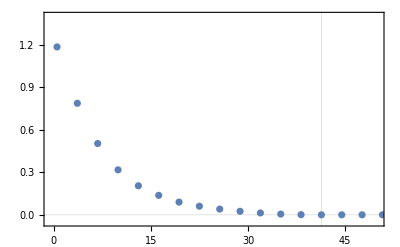

```mathematica
(*Negativities*)
figneg=Show[ListPlot[{wn},PlotRange->{{-0.5,50},{-0.05,1.4}},Joined->False,Frame->True,GridLines->{{13*π+0.5},{0}},GridLinesStyle->{{Black,Dashed,Thick},{}},LabelStyle->{Black,16}]]
```

```mathematica
LNeg1={{0.05,6π},{0.04,7π},{0.03,9π},{0.02,13π},{0.01,28π}};
LNeg2={{0.01,20π},{0.02,10π},{0.03,7π},{0.04,5π},{0.05,4π}};
```

```mathematica
N[13π]
```

40.8407

```mathematica
N[10π]
```

31.4159

```mathematica
fit1=NonlinearModelFit[LNeg1,d*Exp[-(a+b*x)/(1+d*x)],{a,b,c,d},x];
fit2=NonlinearModelFit[LNeg2,d*Exp[-(a+b*x)/(1+d*x)],{a,b,c,d},x];
```

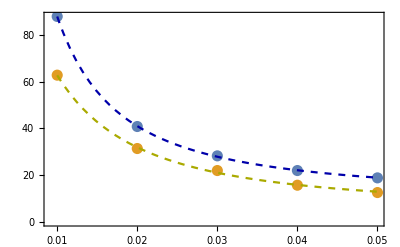

```mathematica
negvsgamma=Show[ListPlot[{LNeg1,LNeg2},Joined->False,Frame->True,PlotStyle->{PointSize[0.02]},LabelStyle->{Black,16}],Plot[fit1[x],{x,0.01,0.05},PlotStyle->{Darker[Blue],Dashed}],Plot[fit2[x],{x,0.01,0.05},PlotStyle->{Darker[Yellow],Dashed}]]
```

```mathematica
Export["Negvsgamma.png",negvsgamma]
```

Negvsgamma.png

#### Survival amplitude

```mathematica
datsp=datasp;
```

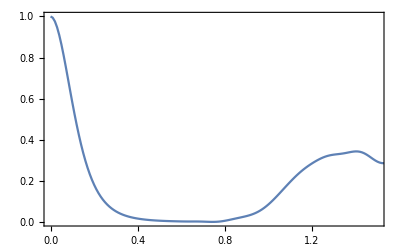

```mathematica
(*Survival probability*)
figsp=Show[ListPlot[{datsp},PlotRange->{{0,1.5},All},Joined->True,Frame->True,GridLines->{{},{}},GridLinesStyle->{{Dashed,Red,Thickness[0.007]},{}},LabelStyle->{Black,18}]]
```

```mathematica
Export["SP_openKerr.png",figsp]
```

SP_openKerr.png

```mathematica
(*Loschmidt echo*)
k=0.01;
ampcomp=Table[datale[[i,2]]+I*datale[[i,3]],{i,1,Length[datale]}];
ampcomp2=Table[datale[[i,3]]+I*datale[[i,4]],{i,1,Length[datale]}];
dataLEtr=Table[{datale[[i,1]],-k*Log[Abs[ampcomp[[i]]]^2]},{i,1,Length[datale]}];
dataLEuhlman=Table[{datale[[i,1]],-k*Log[Abs[ampcomp2[[i]]]^2]},{i,1,Length[datale]}];
```

```mathematica
k=0.05;
dataSA=Import["output/survivalamplitudetest.dat"];
ampcomp3=Table[dataSA[[i,2]]+I*dataSA[[i,3]],{i,1,Length[dataSA]}];
dataEX=Table[{dataSA[[i,1]],-k*Log[Abs[ampcomp3[[i]]]^2]},{i,1,Length[dataSA]}];
```

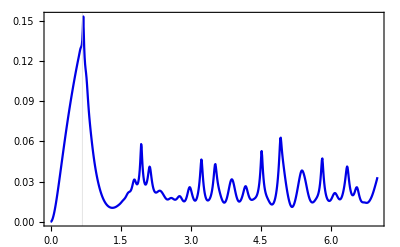

```mathematica
figsa=ListPlot[{dataLEuhlman},PlotRange->{{0,7},All},PlotStyle->{Darker[Blue,0.1],{Darker[Green,0.1],Dashed},{Darker[Red,0.1],Dashed}},PlotLegends->{},Frame->True,Joined->True,LabelStyle->{18,Black},FrameLabel->{},GridLines->{{0.68},{}},GridLinesStyle->{{Dashed,Red,Thickness[0.007]},{Thick,Red,Dashed}}]
```

```mathematica
Export["LE_openKerr.png",figsa]
```

LE_openKerr.png

```mathematica
ampcomp=Table[datasact[[i,3]]+I*datasact[[i,4]],{i,1,Length[datasact]}];
datact=Table[{datasact[[i,2]],datasact[[i,1]],Log[Abs[ampcomp[[i]]]^2]},{i,1,Length[datasact]}];
```

```mathematica
fig2=ListDensityPlot[datact,GridLines->{{0},{}},LabelStyle->{18,Black},GridLinesStyle->{{Dashed,Black,Thick},{Thick,Red,Dashed}},PlotRange->{{-0.1,0.1},{0,10},{-15,15}},PlotLegends->Automatic,ColorFunction->"TemperatureMap",LabelStyle->"Subtitle"]
```

-Graphics-

```mathematica
FindMinimum[10*x^2-x^4,{x,0.2}]
```

{1.56081×10^-24,{x→3.95071×10^-13}}

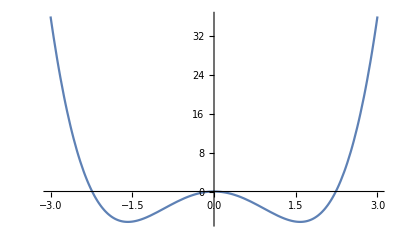

```mathematica
Plot[-5*x^2+x^4,{x,-3,3}]
```